```mathematica
(*The Role of Adaptive Reformulation for Improving Electrochemical Thermal Simulation of Lithium-Ion Batteries*)
(*Copyright@2020 VPSL group (LeXu,Email:lexu@cqu.edu.cn),Chongqing University.All Rights Reserved.*)


(*Firstly,please set the directory.*)
(*When you download the ‘Electrochemical-Thermal-Simulation-main.zip’ from github,you should put it in one of your disks and unzip it.*)(*For instance,if you put it in G disk,the directory should be set as follows:*)
SetDirectory["G:\\Electrochemical-Thermal-Simulation-main\\Electrochemical-Thermal-Simulation-main\\Data"];


Needs["Notation`"];
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
Clear["Global`*"];(*Clear all variables*)

(*Import the reference values==============================*)
(*In this study,the freely available LIONSIMBA toolbox is used as the benchmark.*)(*The LIONSIMBA toolbox can be found in https://github.com/lionsimbatoolbox/LIONSIMBA.*)

refVt=Import["refVt_2C.CSV"];
refVt=refVt[[2;;-1,2]];


simtime=1360;

(*Number of discrete nodes*)
(*Subscript[Nt, p]: Cathode*)
(*Subscript[Nt, s]: Separator*)
(*Subscript[Nt, n]: Anode*)
Subscript[Nt, p]=7;
Subscript[Nt, s]=4;
Subscript[Nt, n]=7;


iapp=-30*2;
Rp=0.2*10^-5;
Rn=0.2*10^-5;

brugg=4;De=0.75*10^-9;Dsp=0.1*10^-13;Dsn=0.39*10^-13;Subscript[eps, p]=.385;Subscript[eps, s]=.724;Subscript[eps, n]=.485;Subscript[Deff, p]=De*Subscript[eps, p]^brugg;Subscript[Deff, s]=De*Subscript[eps, s]^brugg;Subscript[Deff, n]=De*Subscript[eps, n]^brugg;Subscript[l, p]=0.80*10^-4;Subscript[l, s]=0.25*10^-4;Subscript[l, n]=0.88*10^-4;Subscript[epsf, p]=0.25*10^-1;Subscript[epsf, n]=0.326*10^-1;ap=(3*(1-Subscript[eps, p]-Subscript[epsf, p]))/Rp;an=(3*(1-Subscript[eps, n]-Subscript[epsf, n]))/Rn;tplus=.363;Subscript[sig, p]=100;Subscript[sig, n]=100;Subscript[sigeff, p]=Subscript[sig, p]*(1-Subscript[eps, p]-Subscript[epsf, p]);Subscript[sigeff, n]=Subscript[sig, n]*(1-Subscript[eps, n]-Subscript[epsf, n]);F=96487;

Subscript[csmax, p]=51554;
Subscript[csmax, n]=30555;
ce=1000;

Subscript[keff, p]=Table[Subscript[kkeff, p][i][t],{i,1,Subscript[Nt, p]+2+1}];
Subscript[keff, s]=Table[Subscript[kkeff, s][i][t],{i,1,Subscript[Nt, s]+2+1}];
Subscript[keff, n]=Table[Subscript[kkeff, n][i][t],{i,1,Subscript[Nt, n]+2+1}];
```

```mathematica
(*2、Pade Matrix==============================*)
(*See methods part: Padé formulation for solid-phase diffusion equation.*)
An={{0,0,0,0},{0,-0.196905943204083,0,0},{0,0,-4.95238152144722,0},{0,0,0,-0.642212535348694}};
Bn={-1500000.00000000,0.0183089976636328,1.19657502957323,-0.214884027236866};
Cn={1,-54710238.2574182,-11694328.0685018,7004566.32592005};

Ap={{0,0,0,0},{0,-0.0504887033856623,0,0},{0,0,-1.26984141575570,0},{0,0,0,-0.164669880858639}};
Bp={-1500000.00000000,0.0183089976636328,1.19657502957323,-0.214884027236866};
Cp={1,-54710238.2574182,-11694328.0685018,7004566.32592005};
```

```mathematica
alpha=0;
beta=0;
NN=Subscript[Nt, s]+1;
g[1]=(beta+1)/(alpha+beta+2);
listg=Table[.5*(1-(alpha^2-beta^2)/((2*i+alpha+beta-1)^2-1)),{i,2,NN}];

g=Prepend[listg,g[1]];
h[1]=0;
h[2]=(alpha+1)*(beta+1)/((alpha+beta+2)^2*(alpha+beta+3));
listh=Table[(i-1)*(i+alpha-1)*(i+beta-1)*(i+alpha+beta-1)/((2*i+alpha+beta-1)*(2*i+alpha+beta-2)^2*(2*i+alpha+beta-3)),{i,3,NN}];
listh=Prepend[listh,h[2]];
h=Prepend[listh,h[1]];
lam=RecurrenceTable[{lam[i+1]==(NN-i+1)*(NN+i+alpha+beta)*lam[i-1+1]/(i*(i+beta)),lam[1]==1},lam,{i,1,NN+1}];
p[1]=2;
p[2]=1;
p[3]=(x-g[[1]])*p[2]-h[[1]]*p[1];
p[4]=(x-g[[2]])*p[3]-h[[2]]*p[2];
For[i=3,i<=NN,i++,p[i+2]=(x-g[[i]])*p[i+2-1]-h[[i]]*p[i+2-2]];
P=lam[[NN+1]]*p[NN+2];
x2=Solve[P==0,x];

x2={0,Table[x2[[i,1,2]],{i,1,NN}],1};
x2=Flatten[x2];


Clear[g,h,lam];
sysab=1;
alpha=0;
beta=sysab;
NN=Subscript[Nt, p]+1;
g[1]=(beta+1)/(alpha+beta+2);
listg=Table[.5*(1-(alpha^2-beta^2)/((2*i+alpha+beta-1)^2-1)),{i,2,NN}];

g=Prepend[listg,g[1]];
h[1]=0;
h[2]=(alpha+1)*(beta+1)/((alpha+beta+2)^2*(alpha+beta+3));
listh=Table[(i-1)*(i+alpha-1)*(i+beta-1)*(i+alpha+beta-1)/((2*i+alpha+beta-1)*(2*i+alpha+beta-2)^2*(2*i+alpha+beta-3)),{i,3,NN}];
listh=Prepend[listh,h[2]];
h=Prepend[listh,h[1]];

lam[1]=1;
For[i=1,i<=NN,i++,lam[i+1]=(NN-i+1)*(NN+i+alpha+beta)*lam[i-1+1]/(i*(i+beta))];
p[1]=2;
p[2]=1;
p[3]=(x-g[[1]])*p[2]-h[[1]]*p[1];
p[4]=(x-g[[2]])*p[3]-h[[2]]*p[2];
For[i=3,i<=NN,i++,p[i+2]=(x-g[[i]])*p[i+2-1]-h[[i]]*p[i+2-2]];
P=lam[NN+1]*p[NN+2];
x1=Solve[P==0,x];

x1={0,Table[x1[[i,1,2]],{i,1,NN}],1};
x1=Flatten[x1];
Clear[g,h,lam];
alpha=sysab;
beta=0;
NN=Subscript[Nt, n]+1;
g[1]=(beta+1)/(alpha+beta+2);
listg=Table[.5*(1-(alpha^2-beta^2)/((2*i+alpha+beta-1)^2-1)),{i,2,NN}];

g=Prepend[listg,g[1]];
h[1]=0;
h[2]=(alpha+1)*(beta+1)/((alpha+beta+2)^2*(alpha+beta+3));
listh=Table[(i-1)*(i+alpha-1)*(i+beta-1)*(i+alpha+beta-1)/((2*i+alpha+beta-1)*(2*i+alpha+beta-2)^2*(2*i+alpha+beta-3)),{i,3,NN}];
listh=Prepend[listh,h[2]];
h=Prepend[listh,h[1]];

lam[1]=1;
For[i=1,i<=NN,i++,lam[i+1]=(NN-i+1)*(NN+i+alpha+beta)*lam[i-1+1]/(i*(i+beta))];
p[1]=2;
p[2]=1;
p[3]=(x-g[[1]])*p[2]-h[[1]]*p[1];
p[4]=(x-g[[2]])*p[3]-h[[2]]*p[2];
For[i=3,i<=NN,i++,p[i+2]=(x-g[[i]])*p[i+2-1]-h[[i]]*p[i+2-2]];
P=lam[NN+1]*p[NN+2];
x3=Solve[P==0,x];
x3={0,Table[x3[[i,1,2]],{i,1,NN}],1};
x3=Flatten[x3];




Nt1=Subscript[Nt, p]+2;
Nt2=Subscript[Nt, s]+2;
Subscript[N, p]=Subscript[Nt, p]+2;
Subscript[N, s]=Subscript[Nt, s]+2;
Subscript[N, n]=Subscript[Nt, n]+2;








c11={2,Table[1,{i,1,Subscript[N, p]-1}],2};
c11=Flatten[c11,1];
c12=Table[(-1)^i,{i,0,Subscript[N, p]}];
c1=c11*c12;
X1=Table[x1,{i,1,Subscript[N, p]+1}];
X1=Transpose[X1];

dX1=X1-Transpose[X1];

D1=(Transpose[{c1}].{1/c1})/(dX1+IdentityMatrix[Subscript[N, p]+1]);
D1=N[D1,8];
D1=D1-DiagonalMatrix[Total[Transpose[D1],1]];

c21={2,Table[1,{i,1,Subscript[N, s]-1}],2};
c21=Flatten[c21,1];
c22=Table[(-1)^i,{i,0,Subscript[N, s]}];
c2=c21*c22;
X2=Table[x2,{i,1,Subscript[N, s]+1}];
X2=Transpose[X2];
dX2=X2-Transpose[X2];
D2=(Transpose[{c2}].{1/c2})/(dX2+IdentityMatrix[Subscript[N, s]+1]);
D2=N[D2,8];
D2=D2-DiagonalMatrix[Total[Transpose[D2],1]];
c31={2,Table[1,{i,1,Subscript[N, n]-1}],2};
c31=Flatten[c31,1];
c32=Table[(-1)^i,{i,0,Subscript[N, n]}];
c3=c31*c32;
X3=Table[x3,{i,1,Subscript[N, n]+1}];
X3=Transpose[X3];
dX3=X3-Transpose[X3];
D3=(Transpose[{c3}].{1/c3})/(dX3+IdentityMatrix[Subscript[N, n]+1]);
D3=N[D3,8];
D3=D3-DiagonalMatrix[Total[Transpose[D3],1]];
Subscript[D1, 2]=D1.D1;
Subscript[D2, 2]=D2.D2;
Subscript[D3, 2]=D3.D3;

x1=N[x1,8];
x2=N[x2,8];
x3=N[x3,8];
```

```mathematica
u10=Table[1000,{i,1,Nt1+1}];
u20=Table[1000,{i,1,Nt2+1}];
u30=Table[1000,{i,1,Nt1+1}];
u1=Table[vu1[i][t],{i,1,Nt1+1}];
u2=Table[vu2[i][t],{i,1,Nt2+1}];
u3=Table[vu3[i][t],{i,1,Nt1+1}];



u4={Table[vu41[i][t],{i,1,Nt1+1}],Table[vu42[i][t],{i,1,Nt1+1}],Table[vu43[i][t],{i,1,Nt1+1}],Table[vu44[i][t],{i,1,Nt1+1}]};

u5={Table[vu51[i][t],{i,1,Nt1+1}],Table[vu52[i][t],{i,1,Nt1+1}],Table[vu53[i][t],{i,1,Nt1+1}],Table[vu54[i][t],{i,1,Nt1+1}]};


z1=Table[vz1[i][t],{i,1,Nt1+1}];

z2=Table[vz2[i][t],{i,1,Nt1+1}];


z3=Table[vz3[i][t],{i,1,Nt1+1}];

z4=Table[vz4[i][t],{i,1,Nt1+1}];

z5=Table[vz5[i][t],{i,1,Nt1+1}];
z6=Table[vz6[i][t],{i,1,Nt2+1}];
z7=Table[vz7[i][t],{i,1,Nt1+1}];




(*cs/csmax*)
Subscript[theta, p]=z1/Subscript[csmax, p];
Subscript[theta, n]=z2/Subscript[csmax, n];


num=-4.656+88.669*Subscript[theta, p]^2-401.119*Subscript[theta, p]^4+342.909*Subscript[theta, p]^6-462.471*Subscript[theta, p]^8+433.434*Subscript[theta, p]^10;den=-1+18.933*Subscript[theta, p]^2-79.532*Subscript[theta, p]^4+37.311*Subscript[theta, p]^6-73.083*Subscript[theta, p]^8+95.96*Subscript[theta, p]^10;fUp=num/den;
fUn=.7222+.1387*Subscript[theta, n]+0.029*Subscript[theta, n]^.5-0.0172/Subscript[theta, n]+0.0019/(Subscript[theta, n]^1.5)+.2808*Exp[.9-15*Subscript[theta, n]]-.7984*Exp[.4465*Subscript[theta, n]-.4108];
```

```mathematica
kp=0.2334*10^-10;
kn=0.5031*10^-10;
R=8.314;
T=298.15;
```

```mathematica
q=500000;
tini=1;
mu=0.00001;
TH=1/2*(1+Tanh[q*(t-tini)]);
```

```mathematica
aa1=({{1,0},{0,-Subscript[Deff, p]/Subscript[l, p]}}.D1[[{1,Nt1+1},{1,Nt1+1}]]);
aa2={{0},{ff1}}-{{1,0},{0,-Subscript[Deff, p]/Subscript[l, p]}}.D1[[{1,Nt1+1},2;;Nt1]].Transpose[{u1[[2;;Nt1]]}];
aa=Inverse[aa1].aa2;
u11=aa[[1]];
u1end=aa[[2]];

aa1=({{-Subscript[Deff, s]/Subscript[l, s],0},{0,-Subscript[Deff, s]/Subscript[l, s]}}.D2[[{1,Nt2+1},{1,Nt2+1}]]);
aa2={{ff1},{ff2}}-{{-Subscript[Deff, s]/Subscript[l, s],0},{0,-Subscript[Deff, s]/Subscript[l, s]}}.D2[[{1,Nt2+1},2;;Nt2]].Transpose[{u2[[2;;Nt2]]}];
aa=Inverse[aa1].aa2;
u21=aa[[1]];
u2end=aa[[2]];

aa1=({{-Subscript[Deff, n]/Subscript[l, n],0},{0,1}}.D3[[{1,Nt1+1},{1,Nt1+1}]]);
aa2={{ff2},{0}}-{{-Subscript[Deff, n]/Subscript[l, n],0},{0,1}}.D3[[{1,Nt1+1},2;;Nt1]].Transpose[{u3[[2;;Nt1]]}];
aa=Inverse[aa1].aa2;
u31=aa[[1]];
u3end=aa[[2]];
```

```mathematica
fun1=u1end-u21==0;
fun2=u2end-u31==0;
var={ff1,ff2};
sol=Solve[{fun1,fun2},var];

ff1=sol[[1,1,2]];
ff2=sol[[1,2,2]];




Subscript[subkeff, p]=Subscript[eps, p]^brugg*(0.41253*10^-1+0.5007*10^-3*u1-0.47212*10^-6*u1^2+0.15094*10^-9*u1^3-0.16018*10^-13*u1^4);
Subscript[subkeff, s]=Subscript[eps, s]^brugg*(0.41253*10^-1+0.5007*10^-3*u2-0.47212*10^-6*u2^2+0.15094*10^-9*u2^3-0.16018*10^-13*u2^4);
Subscript[subkeff, n]=Subscript[eps, n]^brugg*(0.41253*10^-1+0.5007*10^-3*u3-0.47212*10^-6*u3^2+0.15094*10^-9*u3^3-0.16018*10^-13*u3^4);
```

```mathematica
aa1=({{1,0},{0,1}}.D1[[{1,Nt1+1},{1,Nt1+1}]]);
aa2={{-iapp*Subscript[l, p]/Subscript[sigeff, p]},{0}}-{{1,0},{0,1}}.D1[[{1,Nt1+1},2;;Nt1]].Transpose[{z3[[2;;Nt1]]}];
aa=Inverse[aa1].aa2;
z31=aa[[1]];
z3end=aa[[2]];


aa1=({{1,0},{0,1}}.D3[[{1,Nt1+1},{1,Nt1+1}]]);
aa2={{0},{-iapp*Subscript[l, n]/Subscript[sigeff, n]}}-{{1,0},{0,1}}.D3[[{1,Nt1+1},2;;Nt1]].Transpose[{z4[[2;;Nt1]]}];
aa=Inverse[aa1].aa2;
z41=aa[[1]];
z4end=aa[[2]];
```

```mathematica
Clear[f1,f2];
aa1=({{1,0},{0,-Subscript[keff, p][[Nt1+1]]/Subscript[l, p]}}.D1[[{1,Nt1+1},{1,Nt1+1}]]);
aa2={{0},{f1}}-{{1,0},{0,-Subscript[keff, p][[Nt1+1]]/Subscript[l, p]}}.D1[[{1,Nt1+1},2;;Nt1]].Transpose[{z5[[2;;Nt1]]}];
aa=Inverse[aa1].aa2;
z51=aa[[1]];
z5end=aa[[2]];


aa1=({{-Subscript[keff, s][[1]]/Subscript[l, s],0},{0,-Subscript[keff, s][[Nt2+1]]/Subscript[l, s]}}.D2[[{1,Nt2+1},{1,Nt2+1}]]);
aa2={{f1},{f2}}-{{-Subscript[keff, s][[1]]/Subscript[l, s],0},{0,-Subscript[keff, s][[Nt2+1]]/Subscript[l, s]}}.D2[[{1,Nt2+1},2;;Nt2]].Transpose[{z6[[2;;Nt2]]}];
aa=Inverse[aa1].aa2;
z61=aa[[1]];
z6end=aa[[2]];


aa1=({{0,0},{0,1}}+{{-Subscript[keff, n][[1]]/Subscript[l, n],0},{0,0}}.D3[[{1,Nt1+1},{1,Nt1+1}]]);
aa2={{f2},{0}}-{{-Subscript[keff, n][[1]]/Subscript[l, n],0},{0,0}}.D3[[{1,Nt1+1},2;;Nt1]].Transpose[{z7[[2;;Nt1]]}];
aa=Inverse[aa1].aa2;
z71=aa[[1]];
z7end=aa[[2]];

fun1=z5end-z61==0;
fun2=z6end-z71==0;
var={f1,f2};
sol=Solve[{fun1,fun2},var];

f1=sol[[1,1,2]];
f2=sol[[1,2,2]];



jjp=2*kp*u1^0.5*z1^0.5*(Subscript[csmax, p]-z1)^0.5*Sinh[.5*F*(z3-z5-fUp)/(R*T)];
jjn=2*kn*u3^0.5*z2^0.5*(Subscript[csmax, n]-z2)^0.5*Sinh[.5*F*(z4-z7-fUn)/(R*T)];
```

```mathematica
du1=(Subscript[Deff, p]/Subscript[l, p]^2*Subscript[D1, 2].u1+ap*(1-tplus)*jjp)/Subscript[eps, p];
du2=(Subscript[Deff, s]/Subscript[l, s]^2*Subscript[D2, 2].u2)/Subscript[eps, s];
du3=(Subscript[Deff, n]/Subscript[l, n]^2*Subscript[D3, 2].u3+an*(1-tplus)*jjn)/Subscript[eps, n];

du1[[1]]=D[u11,t][[1]];
du1[[Nt1+1]]=D[u1end,t][[1]];
fodelhs1=D[u1,t];
fode1=Table[fodelhs1[[i]]-du1[[i]]*TH==0,{i,1,Nt1+1}];
fode1=Flatten[fode1];



du2[[1]]=D[u21,t][[1]];
du2[[Nt2+1]]=D[u2end,t][[1]];
fodelhs2=D[u2,t];
fode2=Table[fodelhs2[[i]]-du2[[i]]*TH==0,{i,1,Nt2+1}];
fode2=Flatten[fode2];



du3[[1]]=D[u31,t][[1]];
du3[[Nt1+1]]=D[u3end,t][[1]];
fodelhs3=D[u3,t];
fode3=Table[fodelhs3[[i]]-du3[[i]]*TH==0,{i,1,Nt1+1}];
fode3=Flatten[fode3];



fode1=fode1/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
fode1=fode1/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
fode1=fode1/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];
fode1=fode1/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
fode1=fode1/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
fode1=fode1/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];



fode2=fode2/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
fode2=fode2/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
fode2=fode2/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];
fode2=fode2/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
fode2=fode2/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
fode2=fode2/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];

fode3=fode3/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
fode3=fode3/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
fode3=fode3/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];
fode3=fode3/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
fode3=fode3/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
fode3=fode3/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];



du41=u4[[1,1;;Nt1+1]]*Ap[[1,1]]+jjp*Bp[[1]];
du42=u4[[2,1;;Nt1+1]]*Ap[[2,2]]+jjp*Bp[[2]];
du43=u4[[3,1;;Nt1+1]]*Ap[[3,3]]+jjp*Bp[[3]];
du44=u4[[4,1;;Nt1+1]]*Ap[[4,4]]+jjp*Bp[[4]];


du51=u5[[1,1;;Nt1+1]]*An[[1,1]]+jjn*Bn[[1]];
du52=u5[[2,1;;Nt1+1]]*An[[2,2]]+jjn*Bn[[2]];
du53=u5[[3,1;;Nt1+1]]*An[[3,3]]+jjn*Bn[[3]];
du54=u5[[4,1;;Nt1+1]]*An[[4,4]]+jjn*Bn[[4]];

fodelhs4=D[u4,t];
fode41=Table[fodelhs4[[1,i]]-du41[[i]]*TH==0,{i,1,Nt1+1}];
fode42=Table[fodelhs4[[2,i]]-du42[[i]]*TH==0,{i,1,Nt1+1}];
fode43=Table[fodelhs4[[3,i]]-du43[[i]]*TH==0,{i,1,Nt1+1}];
fode44=Table[fodelhs4[[4,i]]-du44[[i]]*TH==0,{i,1,Nt1+1}];

fode4={fode41,fode42,fode43,fode44};
fode4=Flatten[fode4];

fode4=fode4/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
fode4=fode4/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
fode4=fode4/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];


fodelhs5=D[u5,t];
fode51=Table[fodelhs5[[1,i]]-du51[[i]]*TH==0,{i,1,Nt1+1}];
fode52=Table[fodelhs5[[2,i]]-du52[[i]]*TH==0,{i,1,Nt1+1}];
fode53=Table[fodelhs5[[3,i]]-du53[[i]]*TH==0,{i,1,Nt1+1}];
fode54=Table[fodelhs5[[4,i]]-du54[[i]]*TH==0,{i,1,Nt1+1}];

fode5={fode51,fode52,fode53,fode54};
fode5=Flatten[fode5];

fode5=fode5/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
fode5=fode5/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
fode5=fode5/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];


fae1=Table[z1[[i]]-(u4[[1,i]]*Cp[[1]]+u4[[2,i]]*Cp[[2]]+u4[[3,i]]*Cp[[3]]+u4[[4,i]]*Cp[[4]]),{i,1,Nt1+1}];
(*负极*)
fae2=Table[z2[[i]]-(u5[[1,i]]*Cn[[1]]+u5[[2,i]]*Cn[[2]]+u5[[3,i]]*Cn[[3]]+u5[[4,i]]*Cn[[4]]),{i,1,Nt1+1}];



fae3=Subscript[sigeff, p]*Subscript[D1, 2].z3/Subscript[l, p]^2-(ap*F*jjp);
fae4=Subscript[sigeff, n]*Subscript[D3, 2].z4/Subscript[l, n]^2-(an*F*jjn);
fae5=-Subscript[sigeff, p]/Subscript[l, p]*D1.z3-Subscript[keff, p]/Subscript[l, p]*D1.z5+2*Subscript[keff, p]*R*T/F*(1-tplus)/Subscript[l, p]*(D1.u1)/u1-iapp;
fae6=-Subscript[keff, s]/Subscript[l, s]*D2.z6+2*Subscript[keff, s]*R*T/F*(1-tplus)/Subscript[l, s]*(D2.u2)/u2-iapp;
fae7=-Subscript[sigeff, n]/Subscript[l, n]*D3.z4-Subscript[keff, n]/Subscript[l, n]*D3.z7+2*Subscript[keff, n]*R*T/F*(1-tplus)/Subscript[l, n]*(D3.u3)/u3-iapp;


fae3[[1]]=vz3[1][t]-z31[[1]];
fae3[[Nt1+1]]=vz3[Nt1+1][t]-z3end[[1]];
fae4[[1]]=vz4[1][t]-z41[[1]];
fae4[[Nt1+1]]=vz4[Nt1+1][t]-z4end[[1]];


fae5[[1]]=vz5[1][t]-z51[[1]];
fae5[[Nt1+1]]=vz5[Nt1+1][t]-z5end[[1]];
fae6[[1]]=vz6[1][t]-z61[[1]];
fae6[[Nt2+1]]=vz6[Nt2+1][t]-z6end[[1]];
fae7[[1]]=vz7[1][t]-z71[[1]];
fae7[[Nt1+1]]=vz7[Nt1+1][t]-z7end[[1]];



dfae1=mu*D[fae1,t];
dfae2=mu*D[fae2,t];
dfae3=mu*D[fae3,t];

dfae4=mu*D[fae4,t];


dfae5=mu*D[fae5,t];

dfae6=mu*D[fae6,t];

dfae7=mu*D[fae7,t];





Subscript[thamax, p]=.4955;
Subscript[thamax, n]=.85510;

Subscript[thamin, p]=1;
Subscript[thamin, n]=0;
soc=0.99999;
Subscript[csave, p]:=(soc*(Subscript[thamax, p]-Subscript[thamin, p])+Subscript[thamin, p])*Subscript[csmax, p];
Subscript[csave, n]:=(soc*(Subscript[thamax, n]-Subscript[thamin, n])+Subscript[thamin, n])*Subscript[csmax, n];


subtiming1=Timing[




dfae1=dfae1/.Flatten[{Table[vu41[i]'[t]->du41[[i]],{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vu42[i]'[t]->du42[[i]],{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vu43[i]'[t]->du43[[i]],{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vu44[i]'[t]->du44[[i]],{i,1,Nt1+1}]}];

dfae1=dfae1/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae1=dfae1/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];



dfae1=dfae1/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vu2[i][t]->1000,{i,1,Nt2+1}]}];
dfae1=dfae1/.Flatten[{Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz3[i][t]->4,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz4[i][t]->0.01,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz5[i][t]->-0.15,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz6[i][t]->-0.05,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];

dfae1=dfae1/.Flatten[{Table[vu41[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];

dfae1=dfae1/.Flatten[{Table[vu42[i][t]->0,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vu43[i][t]->0,{i,1,Nt1+1}]}];
dfae1=dfae1/.Flatten[{Table[vu44[i][t]->0,{i,1,Nt1+1}]}];

];


subtiming2=Timing[
dfae2=dfae2/.Flatten[{Table[vu51[i]'[t]->du51[[i]],{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vu52[i]'[t]->du52[[i]],{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vu53[i]'[t]->du53[[i]],{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vu54[i]'[t]->du54[[i]],{i,1,Nt1+1}]}];


dfae2=dfae2/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae2=dfae2/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];


dfae2=dfae2/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vu2[i][t]->1000,{i,1,Nt2+1}]}];
dfae2=dfae2/.Flatten[{Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz3[i][t]->4,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz4[i][t]->0.01,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz5[i][t]->-0.15,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz6[i][t]->-0.05,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];

dfae2=dfae2/.Flatten[{Table[vu51[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];

dfae2=dfae2/.Flatten[{Table[vu52[i][t]->0,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vu53[i][t]->0,{i,1,Nt1+1}]}];
dfae2=dfae2/.Flatten[{Table[vu54[i][t]->0,{i,1,Nt1+1}]}];

];


subtiming3=Timing[
dfae3=dfae3/.Flatten[{Table[vu1[i]'[t]->du1[[i]],{i,2,Nt1}]}];
dfae3=dfae3/.Flatten[{Table[vu2[i]'[t]->du2[[i]],{i,2,Nt2}]}];
dfae3=dfae3/.Flatten[{Table[vu3[i]'[t]->du3[[i]],{i,2,Nt1}]}];

dfae3=dfae3/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae3=dfae3/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
dfae3=dfae3/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];



dfae3=dfae3/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}]}];


dfae3=dfae3/.Flatten[{Table[vu2[i][t]->1000,{i,1,Nt2+1}]}];
dfae3=dfae3/.Flatten[{Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];

dfae3=dfae3/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[vz3[i][t]->4,{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[vz4[i][t]->0.01,{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[vz5[i][t]->-0.15,{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[vz6[i][t]->-0.05,{i,1,Nt1+1}]}];
dfae3=dfae3/.Flatten[{Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];
];


subtiming4=Timing[
dfae4=dfae4/.Flatten[{Table[vu1[i]'[t]->du1[[i]],{i,2,Nt1}]}];
dfae4=dfae4/.Flatten[{Table[vu2[i]'[t]->du2[[i]],{i,2,Nt2}]}];
dfae4=dfae4/.Flatten[{Table[vu3[i]'[t]->du3[[i]],{i,2,Nt1}]}];


dfae4=dfae4/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae4=dfae4/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
dfae4=dfae4/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];





dfae4=dfae4/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}]}];


dfae4=dfae4/.Flatten[{Table[vu2[i][t]->1000,{i,1,Nt2+1}]}];
dfae4=dfae4/.Flatten[{Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];

dfae4=dfae4/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[vz3[i][t]->4,{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[vz4[i][t]->0.01,{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[vz5[i][t]->-0.15,{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[vz6[i][t]->-0.05,{i,1,Nt1+1}]}];
dfae4=dfae4/.Flatten[{Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];

];


subtiming5=Timing[

dfae5=dfae5/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae5=dfae5/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];


dfae5=dfae5/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
dfae5=dfae5/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];



dfae5=dfae5/.Flatten[{Table[vu1[i]'[t]->du1[[i]],{i,2,Nt1}]}];
dfae5=dfae5/.Flatten[{Table[vu2[i]'[t]->du2[[i]],{i,2,Nt2}]}];
dfae5=dfae5/.Flatten[{Table[vu3[i]'[t]->du3[[i]],{i,2,Nt1}]}];

dfae5=dfae5/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}]}];


dfae5=dfae5/.Flatten[{Table[vu2[i][t]->1000,{i,1,Nt2+1}]}];
dfae5=dfae5/.Flatten[{Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];

dfae5=dfae5/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[vz3[i][t]->4,{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[vz4[i][t]->0.01,{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[vz5[i][t]->-0.15,{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[vz6[i][t]->-0.05,{i,1,Nt1+1}]}];
dfae5=dfae5/.Flatten[{Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];
];


subtiming6=Timing[


dfae6=dfae6/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae6=dfae6/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae6=dfae6/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];


dfae6=dfae6/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
dfae6=dfae6/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
dfae6=dfae6/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];




dfae6=dfae6/.Flatten[{Table[vu1[i]'[t]->du1[[i]],{i,2,Nt1}],Table[vu2[i]'[t]->du2[[i]],{i,2,Nt2}],Table[vu3[i]'[t]->du3[[i]],{i,2,Nt1}]}];



dfae6=dfae6/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}],Table[vu2[i][t]->1000,{i,1,Nt2+1}],Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];





dfae6=dfae6/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}],Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}],Table[vz3[i][t]->4,{i,1,Nt1+1}],Table[vz4[i][t]->0.01,{i,1,Nt1+1}],Table[vz5[i][t]->-0.15,{i,1,Nt1+1}],Table[vz6[i][t]->-0.05,{i,1,Nt1+1}],Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];






];


subtiming7=Timing[

dfae7=dfae7/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
dfae7=dfae7/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];


dfae7=dfae7/.Flatten[{Table[D[Subscript[keff, p][[i]],t]->0,{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[D[Subscript[keff, s][[i]],t]->0,{i,1,Nt2+1}]}];
dfae7=dfae7/.Flatten[{Table[D[Subscript[keff, n][[i]],t]->0,{i,1,Nt1+1}]}];

dfae7=dfae7/.Flatten[{Table[vu1[i]'[t]->du1[[i]],{i,2,Nt1}]}];
dfae7=dfae7/.Flatten[{Table[vu2[i]'[t]->du2[[i]],{i,2,Nt2}]}];
dfae7=dfae7/.Flatten[{Table[vu3[i]'[t]->du3[[i]],{i,2,Nt1}]}];

dfae7=dfae7/.Flatten[{Table[vu1[i][t]->1000,{i,1,Nt1+1}]}];


dfae7=dfae7/.Flatten[{Table[vu2[i][t]->1000,{i,1,Nt2+1}]}];
dfae7=dfae7/.Flatten[{Table[vu3[i][t]->1000,{i,1,Nt1+1}]}];

dfae7=dfae7/.Flatten[{Table[vz1[i][t]->Subscript[csave, p],{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[vz2[i][t]->Subscript[csave, n],{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[vz3[i][t]->4,{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[vz4[i][t]->0.01,{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[vz5[i][t]->-0.15,{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[vz6[i][t]->-0.05,{i,1,Nt1+1}]}];
dfae7=dfae7/.Flatten[{Table[vz7[i][t]->-0.001,{i,1,Nt1+1}]}];


];










ae1=Table[dfae1[[i]]==-fae1[[i]],{i,1,Nt1+1}];
ae2=Table[dfae2[[i]]==-fae2[[i]],{i,1,Nt1+1}];
ae3=Table[dfae3[[i]]==-fae3[[i]],{i,1,Nt1+1}];

ae4=Table[dfae4[[i]]==-fae4[[i]],{i,1,Nt1+1}];

ae5=Table[dfae5[[i]]==-fae5[[i]],{i,1,Nt1+1}];

ae5=ae5/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
ae5=ae5/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
ae5=ae5/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];







ae6=Table[dfae6[[i]]==-fae6[[i]],{i,1,Nt2+1}];


ae6=ae6/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
ae6=ae6/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
ae6=ae6/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];



ae7=Table[dfae7[[i]]==-fae7[[i]],{i,1,Nt1+1}];

ae7=ae7/.Flatten[{Table[Subscript[keff, p][[i]]->Subscript[subkeff, p][[i]],{i,1,Nt1+1}]}];
ae7=ae7/.Flatten[{Table[Subscript[keff, s][[i]]->Subscript[subkeff, s][[i]],{i,1,Nt2+1}]}];
ae7=ae7/.Flatten[{Table[Subscript[keff, n][[i]]->Subscript[subkeff, n][[i]],{i,1,Nt1+1}]}];



AE={ae1,ae2,ae3,ae4,ae5,ae6,ae7};
AE=Flatten[AE];
ODE1=Table[fode1[[i]],{i,1,Nt1+1}];
ODE2=Table[fode2[[i]],{i,1,Nt2+1}];
ODE3=Table[fode3[[i]],{i,1,Nt1+1}];
ODE4=Table[fode4[[i]],{i,1,4*(Nt1+1)}];
ODE5=Table[fode5[[i]],{i,1,4*(Nt1+1)}];

ODE={ODE1,ODE2,ODE3,ODE4,ODE5};
ODE=Flatten[ODE];
icode1=Table[vu1[i][0]==1000,{i,1,Nt1+1}];
icode2=Table[vu2[i][0]==1000,{i,1,Nt2+1}];
icode3=Table[vu3[i][0]==1000,{i,1,Nt1+1}];





icode41=Table[vu41[i][0]==Subscript[csave, p],{i,1,Nt1+1}];
icode42=Table[vu42[i][0]==0,{i,1,Nt1+1}];
icode43=Table[vu43[i][0]==0,{i,1,Nt1+1}];
icode44=Table[vu44[i][0]==0,{i,1,Nt1+1}];


icode4={icode41,icode42,icode43,icode44};
icode4=Flatten[icode4];

icode51=Table[vu51[i][0]==Subscript[csave, n],{i,1,Nt1+1}];
icode52=Table[vu52[i][0]==0,{i,1,Nt1+1}];
icode53=Table[vu53[i][0]==0,{i,1,Nt1+1}];
icode54=Table[vu54[i][0]==0,{i,1,Nt1+1}];


icode5={icode51,icode52,icode53,icode54};
icode5=Flatten[icode5];

icae1=Table[vz1[i][0]==Subscript[csave, p],{i,1,Nt1+1}];
icae2=Table[vz2[i][0]==Subscript[csave, n],{i,1,Nt1+1}];
icae3=Table[vz3[i][0]==4,{i,1,Nt1+1}];
icae4=Table[vz4[i][0]==0.01,{i,1,Nt1+1}];
icae5=Table[vz5[i][0]==-0.15,{i,1,Nt1+1}];
icae6=Table[vz6[i][0]==-0.05,{i,1,Nt2+1}];
icae7=Table[vz7[i][0]==-0.001,{i,1,Nt1+1}];

ic={icode1,icode2,icode3,icode4,icode5,icae1,icae2,icae3,icae4,icae5,icae6,icae7};
ic=Flatten[ic];
var={Table[vu1[i][t],{i,1,Nt1+1}],Table[vu2[i][t],{i,1,Nt2+1}],Table[vu3[i][t],{i,1,Nt1+1}],u4,u5,z1,z2,Table[vz3[i][t],{i,1,Nt1+1}],Table[vz4[i][t],{i,1,Nt1+1}],Table[vz5[i][t],{i,1,Nt1+1}],Table[vz6[i][t],{i,1,Nt2+1}],Table[vz7[i][t],{i,1,Nt1+1}]};
var=Flatten[var];
(*Get simulation time*)
calt=Timing[sol=NDSolve[{ODE,AE,ic},var,{t,0,simtime,0.01},AccuracyGoal->4,Method->{"EquationSimplification"->"Residual"}];];
```

```mathematica
(*extract internal variables*)
tablerey=Table[sol[[1,i,2]]/.t->(j-1),{i,1,10*(Nt1+1)+Nt2+1},{j,1,simtime+1}];
tablerez=Table[sol[[1,i,2]]/.t->(j-1),{i,10*(Nt1+1)+Nt2+1+1,16*(Nt1+1)+2*(Nt2+1)},{j,1,simtime+1}];


(*Voltage*)
outup=Table[tablerez[[i,j]],{i,2*(Nt1+1)+1,2*(Nt1+1)+1},{j,1,simtime+1}];
outun=Table[tablerez[[i,j]],{i,4*(Nt1+1),4*(Nt1+1)},{j,1,simtime+1}];
outup=Flatten[outup];
outun=Flatten[outun];
outVt=outup-outun;
outVt=Partition[outVt,simtime+1]//TableForm;



Export["paderesult_Vt.csv",outVt];



(*RMSE error of Voltage*)

comVt=outVt[[1,1,2;;-1]];
refVt=Flatten[refVt];

comVt=comVt[[2;;-1]];
refVt=refVt[[2;;-1]];
rmseVt=Table[(comVt[[i]]-refVt[[i]])^2,{i,1,simtime-1-10}];
rmseVt=(Mean[rmseVt])^0.5*1000;
```

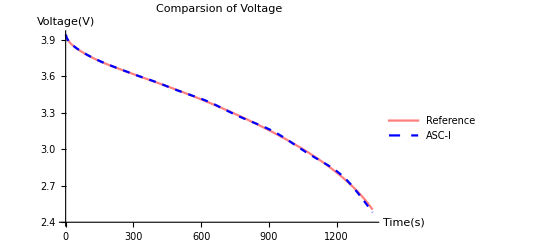

```mathematica
ListLinePlot[{refVt,comVt},PlotStyle->{Directive[Red,Thick,Opacity[0.5]],Directive[Blue,Dashed]},PlotLabel->"Comparsion of Voltage",PlotLegends->LineLegend[{"Reference","ASC-I"},LegendFunction->Frame],AxesLabel->{Time[s],Voltage[V]}]
```

```mathematica
(*Show simulation time and RMSE of voltage*)
calt        (*Simulation time (s)*)
rmseVt   (*RMSE of voltage (mV)*)
```

{0.4375,Null}

5.85309